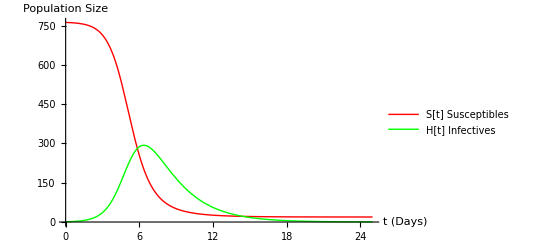

```mathematica
(*Define parameters*)
beta=2.18*10^-3;
gamma=0.44;

(*Define the system of differential equations*)
eqns={S'[t]==-beta*S[t]*H[t],H'[t]==beta*S[t]*H[t]-gamma*H[t],S[0]==762,H[0]==1};

(*Solve the system numerically*)
sol=NDSolve[eqns,{S,H},{t,0,30}];

(*Plot the solutions*)
Plot[Evaluate[{S[t],H[t]}/.sol],{t,0,25},PlotStyle->{Red,Green},PlotLegends->{"S[t] Susceptibles","H[t] Infectives"},AxesLabel->{"t (Days)","Population Size"},AxesStyle->Arrowheads[0.02]]
```

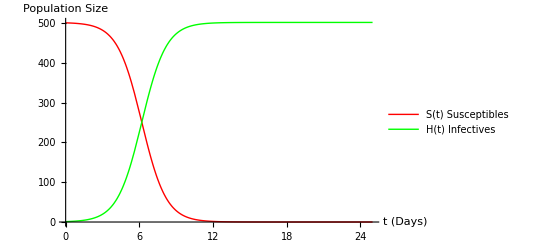

```mathematica
(*Parameters and initial conditions contigous for life*)

beta=0.002;
s0=500;
h0=1;

(*Solve the system numerically*)
solution=NDSolve[{S'[t]==-beta*S[t]*H[t],H'[t]==beta*S[t]*H[t],S[0]==s0,H[0]==h0},{S,H},{t,0,25}];

(*Plot the solution*)
Plot[Evaluate[{S[t],H[t]}/.solution],{t,0,25},AxesLabel->{"t (Days)","Population Size"},PlotStyle->{Red,Green},PlotLegends->Placed[LineLegend[{Red,Green},{"S(t) Susceptibles","H(t) Infectives"}],Above]]
```

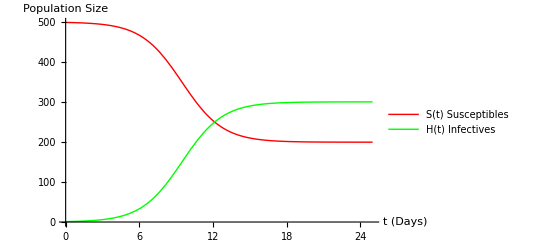

```mathematica
(*Parameters-Disease with Carrier*)
beta=0.002;
gamma=0.4;
s0=500;
h0=1;

(*Solve the system numerically*)
solution=NDSolve[{S'[t]==-beta*S[t]*H[t]+gamma*H[t],H'[t]==beta*S[t]*H[t]-gamma*H[t],S[0]==s0,H[0]==h0},{S,H},{t,0,30}];

(*Plot the solutions*)
Plot[Evaluate[{S[t],H[t]}/.solution],{t,0,25},AxesLabel->{"t (Days)","Population Size"},PlotStyle->{Red,Green},PlotLegends->Placed[LineLegend[{Red,Green},{"S(t) Susceptibles","H(t) Infectives"}],Above]]
```